# Ejemplo Poincaré-Bendixson

Ecuación transformada en sistema


Región atrapante:

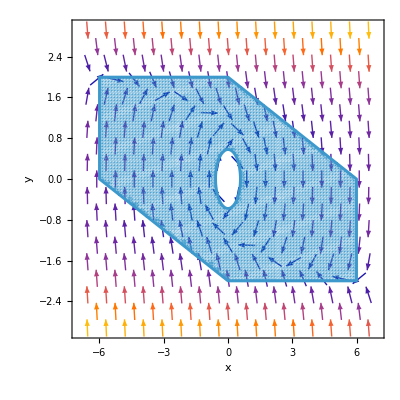

```mathematica
Show[VectorPlot[{y,y*(1-y^2)-x},{x,-7,7},{y,-3,3},FrameLabel->{x,y}],RegionPlot[x>-6&&y<2&&y<-x/3+2&&x<6&&y>-2&&y>-x/3-2&&x^2+y^2>1/3,{x,-7,7},{y,-3,3},PlotPoints->100]]
```

```mathematica
sol1=NDSolve[{x'[t]==y[t],y'[t]==y[t]*(1-y[t]^2)-x[t],x[0]==0,y[0]==-1},{x,y},{t,0,1000}];
```

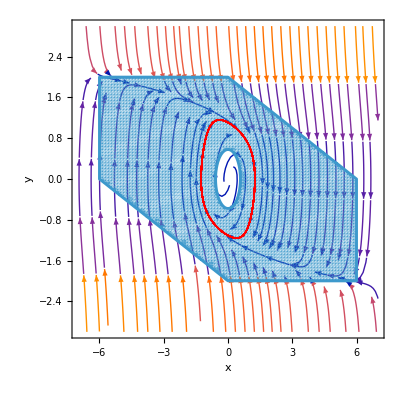

```mathematica
Show[StreamPlot[{y,y*(1-y^2)-x},{x,-7,7},{y,-3,3},FrameLabel->{x,y}],RegionPlot[x>-6&&y<2&&y<-x/3+2&&x<6&&y>-2&&y>-x/3-2&&x^2+y^2>1/3,{x,-7,7},{y,-3,3},PlotPoints->100],ParametricPlot[Evaluate[{x[t],y[t]}/.sol1],{t,900,1000},PlotStyle->{Red,Thick}]]
```